```mathematica
13*0.25/3*2*π//N
13*0.4/3*2*π//N
13*0.24/3*2*π//N
31*0.25/3*2*π//N
```

6.80678

10.8909

6.53451

16.2316

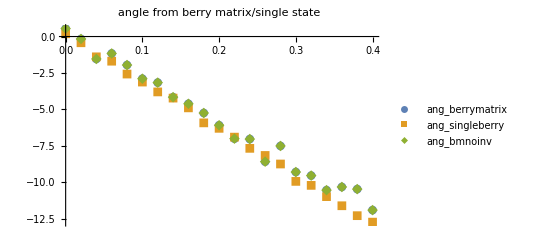

```mathematica
(*ne=10*)
berrymatrix=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_berymatrixne10","Table"];
singleberry=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_singleberryne10","Table"];
bmoninv=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_berymatrix_noinvne10","Table"];
n:=Length[berrymatrix]
x=Table[berrymatrix[[i]][[1]],{i,1,n,1}];
angm= Table[{x[[i]],berrymatrix[[i]][[2]]},{i,1,n}];
angs = Table[{x[[i]],singleberry[[i]][[2]]},{i,1,n}];
angmnoinv = Table[{x[[i]],bmoninv[[i]][[2]]},{i,1,n}];

ListPlot[{angm,angs,angmnoinv},PlotLegends->{"ang_berrymatrix","ang_singleberry", "ang_bmnoinv"},PlotMarkers->Automatic, PlotLabel->"angle from berry matrix/single state"]
```

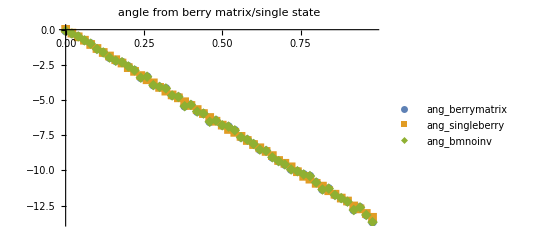

```mathematica
(*ne=4, nMea=100*)
berrymatrix=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_berymatrix","Table"];
singleberry=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_singleberry","Table"];
bmoninv=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/may27_berymatrix_noinv","Table"];
n:=Length[berrymatrix]
x=Table[berrymatrix[[i]][[1]],{i,1,n,1}];
angm= Table[{x[[i]],berrymatrix[[i]][[2]]},{i,1,n}];
angs = Table[{x[[i]],singleberry[[i]][[2]]},{i,1,n}];
angmnoinv = Table[{x[[i]],bmoninv[[i]][[2]]},{i,1,n}];

ListPlot[{angm,angs,angmnoinv},PlotLegends->{"ang_berrymatrix","ang_singleberry", "ang_bmnoinv"},PlotMarkers->Automatic, PlotLabel->"angle from berry matrix/single state"]
```

```mathematica
13*0.25/3*π*2
Mod[%,2π]
```

6.80678

0.523599

```mathematica
bmdual
bmorth
bmnonorth
singleb
```

{{0,-0.11027},{0.02,-0.175529},{0.04,-0.496445},{0.06,-0.861801},{0.08,-1.0478},{0.1,-1.31317},{0.12,-1.63954},{0.14,-2.04834},{0.16,-2.12245},{0.18,-2.34395}}

{{0,-0.11027},{0.02,-0.175529},{0.04,-0.496445},{0.06,-0.861801},{0.08,-1.0478},{0.1,-1.31317},{0.12,-1.63954},{0.14,-2.04834},{0.16,-2.12245},{0.18,-2.34395}}

{{0,-0.11027},{0.02,-0.175529},{0.04,-0.496445},{0.06,-0.861801},{0.08,-1.0478},{0.1,-1.31317},{0.12,-1.63954},{0.14,-2.04834},{0.16,-2.12245},{0.18,-2.34395}}

{{0,-0.0115387},{0.02,-0.261133},{0.04,-0.529695},{0.06,-0.794584},{0.08,-1.09303},{0.1,-1.36617},{0.12,-1.58577},{0.14,-1.86384},{0.16,-2.08786},{0.18,-2.40796}}

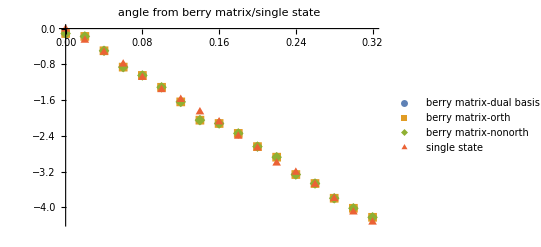

```mathematica
(*ne=4, nMea=100*)
bmdual=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/bm_dualbasis","Table"];
bmorth=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/bm_orth","Table"];
bmnonorth=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/bm_nonorth","Table"];
singleb=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/singleb","Table"];
n:=Length[bmdual]
x=Table[bmdual[[i]][[1]],{i,1,n,1}];
angdual= Table[{x[[i]],bmdual[[i]][[2]]},{i,1,n}];
angorth = Table[{x[[i]],bmorth[[i]][[2]]},{i,1,n}];
angnonorth = Table[{x[[i]],bmnonorth[[i]][[2]]},{i,1,n}];
angsingleb = Table[{x[[i]],singleb[[i]][[2]]},{i,1,n}];

ListPlot[{angdual,angorth,angnonorth, angsingleb},PlotLegends->{"berry matrix-dual basis","berry matrix-orth", "berry matrix-nonorth", "single state"},PlotMarkers->Automatic, PlotLabel->"angle from berry matrix/single state"]
```

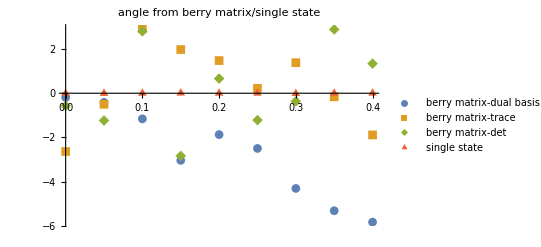

```mathematica
(*ne=4, nMea=10*)
bm=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/berry_matrix","Table"];
singleb=Import["Google Drive/jie_programs/QHlattice/berrymatrix_singlestateberry/berry_single","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n,1}];
angdual= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
angtrace = Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
angdet = Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
angsingleb = Table[{x[[i]],singleb[[i]][[2]]},{i,1,n}];

ListPlot[{angdual,angtrace, angdet, angsingleb},PlotLegends->{"berry matrix-dual basis","berry matrix-trace", "berry matrix-det", "single state"},PlotMarkers->Automatic, PlotLabel->"angle from berry matrix/single state"]
```

```mathematica
13*0.0025/3*2*π
```

0.0680678